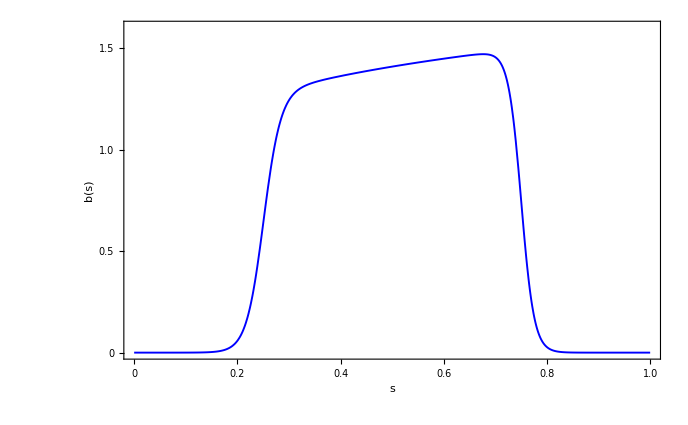

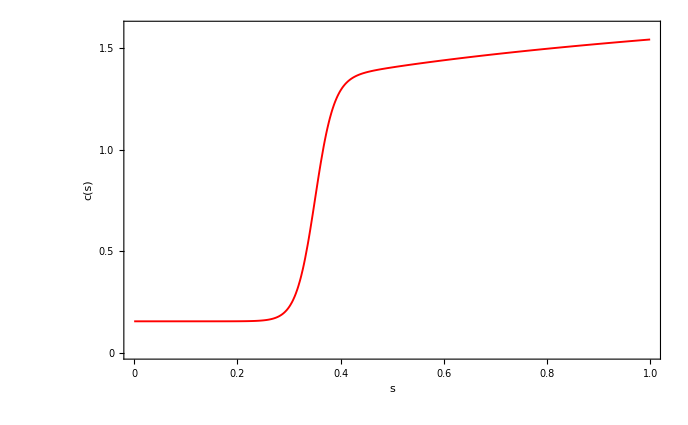

```mathematica
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["Space-Debris-Model.nb",InsertResults->False];
myThickness=0.005;tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.03,.015}][##]&;                                                                                   

b=0.70;
sL=0.15;
sR=0.0;
tauL=0.25;
tauR=0.75;
betaL=60;
betaR=80;

a=0.1;
sc=0.15;
betaC=55.0;
tauC=0.25;

myThickness=0.002;
tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.03,.015}][##]&;

Plot[ben[s,b,sL,sR,tauL,tauR,betaL,betaR],
{s,0,1},
PlotStyle->{{Thickness[myThickness],Blue},{Thickness[myThickness],Red}},
ImagePadding->All,Frame->True,
FrameTicks->{{tickFunc,tickFunc},{tickFunc,tickFunc}},
FrameLabel->{"s"," b(s)"},
Ticks->Automatic,
LabelStyle->Directive[Gray,16],
PlotRange->{{0,1},{0,1.6}}]

Plot[cost[s,0.1,0.35,55.0,0.15],{s,0,1},
PlotStyle->{{Thickness[myThickness],Red},{Thickness[myThickness],Red}},
ImagePadding->All,Frame->True,
FrameTicks->{{tickFunc,tickFunc},{tickFunc,tickFunc}},
FrameLabel->{"s"," c(s)"},
Ticks->Automatic,
LabelStyle->Directive[Gray,16],
PlotRange->{{0,1},{0,1.6}}]
```